```mathematica
Needs["Notation`"];
Notation[Δ ⟺ cd]
Notation[𝒿 ⟺ cj]
```

```mathematica
<<sneg`sneg`;
snegfermionoperators[a,b,c];
snegrealconstants[cj,U,U1,t,t22,t23,cd,x];
```

sneg 1.250 Copyright (C) 2016 Rok Zitko

```mathematica
myop = {a[1],a[2],a[3],a[4],a[5],a[6]}
```

{a^,a[2],a[3],a[4],a[5],a[6]}

```mathematica
makebasis[myop]
```

{a_(1⇑)^†,a_(1↓)^†,a_(2⇑)^†,a_(2↓)^†,a_(3⇑)^†,a_(3↓)^†,a_(4⇑)^†,a_(4↓)^†,a_(5⇑)^†,a_(5↓)^†,a_(6⇑)^†,a_(6↓)^†}

```mathematica
vc6= qszbasisvc[myop];
```

```mathematica
basise4p2 = Select[vc6,#[[1]]=={-2,2}&][[1,2]];
```

```mathematica
basise4p1 = Select[vc6,#[[1]]=={-2,1}&][[1,2]];
```

```mathematica
basise40 = Select[vc6,#[[1]]=={-2,0}&][[1,2]];
```

```mathematica
basise4n1 = Select[vc6,#[[1]]=={-2,-1}&][[1,2]];
```

```mathematica
basise4n2= Select[vc6,#[[1]]=={-2,-2}&][[1,2]];
```

```mathematica
hhop = -t22(hop[a[2],a[5]])- t22(hop[a[3],a[6]])-t23(hop[a[2],a[6]]+hop[a[3],a[5]])
```

-t22 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)-t23 (a_(2↓)^†·a_(6↓)^+a_(2⇑)^†·a_(6⇑)^+a_(3↓)^†·a_(5↓)^+a_(3⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(3↓)^+a_(5⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(2↓)^+a_(6⇑)^†·a_(2⇑)^)-t22 (a_(3↓)^†·a_(6↓)^+a_(3⇑)^†·a_(6⇑)^+a_(6↓)^†·a_(3↓)^+a_(6⇑)^†·a_(3⇑)^)

```mathematica
hhd = cd(number[a[3]]+number[a[6]])(* 0.0(number[a[1]]+number[a[2]]+number[a[4]]+number[a[5]])*)
```

Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)

```mathematica
hhj = (U-3cj)(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])
```

(-3 𝒿+U) (-(a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^)-a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^-a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^-a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^-a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^-a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^-a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^-a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^-a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^-a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^-a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)

```mathematica
hhu = U(hubbard[a[1]]+hubbard[a[2]]+hubbard[a[3]]+hubbard[a[4]]+hubbard[a[5]]+hubbard[a[6]])
```

U (-(a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
hhu1 = (*U1(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])+*)(U-2cj)(nc[number[a[1],UP],number[a[2],DO]]+nc[number[a[1],UP],number[a[3],DO]]+nc[number[a[2],UP],number[a[3],DO]]+nc[number[a[1],DO],number[a[2],UP]]+nc[number[a[1],DO],number[a[3],UP]]+nc[number[a[2],DO],number[a[3],UP]]+nc[number[a[4],UP],number[a[5],DO]]+nc[number[a[4],UP],number[a[6],DO]]+nc[number[a[5],UP],number[a[6],DO]]+nc[number[a[4],DO],number[a[5],UP]]+nc[number[a[4],DO],number[a[6],UP]]+nc[number[a[5],DO],number[a[6],UP]])//Simplify
```

(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)

```mathematica
(* U' = U -2J, since Hamiltonian maintains rotation invariance*)
```

```mathematica
(* pair fliping, hhpf*)
```

```mathematica
hhpf1=nc[a[CR,1,UP],a[AN,1,DO],a[CR,2,DO],a[AN,2,UP]]+nc[a[CR,1,UP],a[AN,1,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,2,UP],a[AN,2,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,5,DO],a[AN,5,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,6,DO],a[AN,6,UP]]+nc[a[CR,5,UP],a[AN,5,DO],a[CR,6,DO],a[AN,6,UP]]
```

-(a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^)-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^

```mathematica
hhpf2=conj[hhpf1]
```

-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^

```mathematica
hhpf=-cj (hhpf1+hhpf2)
```

-𝒿 (-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)

```mathematica
(*pair hopping, hhph*)
```

```mathematica
hhph1=nc[a[CR,1,UP],a[AN,2,UP],a[CR,1,DO],a[AN,2,DO]]+nc[a[CR,1,UP],a[AN,3,UP],a[CR,1,DO],a[AN,3,DO]]+nc[a[CR,2,UP],a[AN,3,UP],a[CR,2,DO],a[AN,3,DO]]+nc[a[CR,4,UP],a[AN,5,UP],a[CR,4,DO],a[AN,5,DO]]+nc[a[CR,4,UP],a[AN,6,UP],a[CR,4,DO],a[AN,6,DO]]+nc[a[CR,5,UP],a[AN,6,UP],a[CR,5,DO],a[AN,6,DO]]
```

-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^

```mathematica
hhph2=conj[hhph1]
```

-(a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^

```mathematica
hhph=-cj (hhph1+hhph2)
```

-𝒿 (-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
ham = hhop + hhu + hhj +hhu1+hhd+hhpf+hhph//Simplify
(*ham= hhop + hhu + hhj +hhu1+hhd*)
```

-t22 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)-t23 (a_(2↓)^†·a_(6↓)^+a_(2⇑)^†·a_(6⇑)^+a_(3↓)^†·a_(5↓)^+a_(3⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(3↓)^+a_(5⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(2↓)^+a_(6⇑)^†·a_(2⇑)^)-t22 (a_(3↓)^†·a_(6↓)^+a_(3⇑)^†·a_(6⇑)^+a_(6↓)^†·a_(3↓)^+a_(6⇑)^†·a_(3⇑)^)+Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^+a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^+a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^+a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^+a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^+a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^+a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^+a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^+a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^+a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)+(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)+(3 𝒿-U) (a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^+a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^+a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^+a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^+a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^+a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^+a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^+a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^+a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^+a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)-U (a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
basise4n1;
```

```mathematica
basise40//Dimensions
basise4n1//Dimensions
basise4n2//Dimensions
basise4p2//Dimensions
basise4p1//Dimensions
```

{225}

{120}

{15}

{15}

{120}

```mathematica
mybasis={basise4n1,basise4n2,basise40,basise4p1,basise4p2}//Flatten;
```

```mathematica
td={cd->0.3,cj->U/5,U->5,t23->x t22,t22->0.3}
```

{Δ→0.3,𝒿→U/5,U→5,t23→t22 x,t22→0.3}

```mathematica
mymat=matrixrepresentationop[ham,mybasis]//.td;
```

```mathematica
vals1=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[1]]},{xx,0,2,0.2}];
vals2=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[2]]},{xx,0,2,0.2}];
vals3=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[3]]},{xx,0,2,0.2}];
vals4=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[4]]},{xx,0,2,0.2}];
vals5=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[5]]},{xx,0,2,0.2}];
vals6=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[6]]},{xx,0,2,0.2}];
vals7=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[7]]},{xx,0,2,0.2}];
vals8=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[8]]},{xx,0,2,0.2}];
vals9=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[9]]},{xx,0,2,0.2}];
vals10=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[10]]},{xx,0,2,0.2}];
```

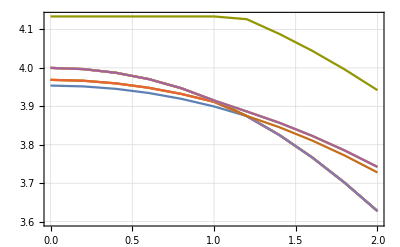

```mathematica
ListLinePlot[{vals1,vals2,vals3,vals4,vals5,vals6,vals7,vals8,vals9,vals10},Frame->True,GridLines->Automatic]
```

```mathematica
(** now we calculate the expection value of the square of spin <|S^2|>, S= s1+s2+s4+s5*)
```

```mathematica
spinpow=spinspin[a[1],a[1]]+spinspin[a[2],a[2]]+spinspin[a[4],a[4]]+spinspin[a[5],a[5]]+2spinspin[a[1],a[2]]+2spinspin[a[1],a[4]]+2spinspin[a[1],a[5]]+2spinspin[a[4],a[5]]+2spinspin[a[2],a[4]]+2spinspin[a[2],a[5]]//Simplify
```

1/4 (3 a_(1↓)^†·a_(1↓)^+3 a_(1⇑)^†·a_(1⇑)^+3 a_(2↓)^†·a_(2↓)^+3 a_(2⇑)^†·a_(2⇑)^+3 a_(4↓)^†·a_(4↓)^+3 a_(4⇑)^†·a_(4⇑)^+3 a_(5↓)^†·a_(5↓)^+3 a_(5⇑)^†·a_(5⇑)^+6 a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^-2 a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+2 a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^-4 a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^-2 a_(1↓)^†·a_(4↓)^†·a_(1↓)^·a_(4↓)^+2 a_(1↓)^†·a_(4⇑)^†·a_(1↓)^·a_(4⇑)^-4 a_(1↓)^†·a_(4⇑)^†·a_(1⇑)^·a_(4↓)^-2 a_(1↓)^†·a_(5↓)^†·a_(1↓)^·a_(5↓)^+2 a_(1↓)^†·a_(5⇑)^†·a_(1↓)^·a_(5⇑)^-4 a_(1↓)^†·a_(5⇑)^†·a_(1⇑)^·a_(5↓)^-4 a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+2 a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^-2 a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-4 a_(1⇑)^†·a_(4↓)^†·a_(1↓)^·a_(4⇑)^+2 a_(1⇑)^†·a_(4↓)^†·a_(1⇑)^·a_(4↓)^-2 a_(1⇑)^†·a_(4⇑)^†·a_(1⇑)^·a_(4⇑)^-4 a_(1⇑)^†·a_(5↓)^†·a_(1↓)^·a_(5⇑)^+2 a_(1⇑)^†·a_(5↓)^†·a_(1⇑)^·a_(5↓)^-2 a_(1⇑)^†·a_(5⇑)^†·a_(1⇑)^·a_(5⇑)^+6 a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-2 a_(2↓)^†·a_(4↓)^†·a_(2↓)^·a_(4↓)^+2 a_(2↓)^†·a_(4⇑)^†·a_(2↓)^·a_(4⇑)^-4 a_(2↓)^†·a_(4⇑)^†·a_(2⇑)^·a_(4↓)^-2 a_(2↓)^†·a_(5↓)^†·a_(2↓)^·a_(5↓)^+2 a_(2↓)^†·a_(5⇑)^†·a_(2↓)^·a_(5⇑)^-4 a_(2↓)^†·a_(5⇑)^†·a_(2⇑)^·a_(5↓)^-4 a_(2⇑)^†·a_(4↓)^†·a_(2↓)^·a_(4⇑)^+2 a_(2⇑)^†·a_(4↓)^†·a_(2⇑)^·a_(4↓)^-2 a_(2⇑)^†·a_(4⇑)^†·a_(2⇑)^·a_(4⇑)^-4 a_(2⇑)^†·a_(5↓)^†·a_(2↓)^·a_(5⇑)^+2 a_(2⇑)^†·a_(5↓)^†·a_(2⇑)^·a_(5↓)^-2 a_(2⇑)^†·a_(5⇑)^†·a_(2⇑)^·a_(5⇑)^+6 a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-2 a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+2 a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^-4 a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-4 a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+2 a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^-2 a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+6 a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
Clear[avs2];
data1={};
Do[
Do[pos1=(Position[Eigensystem[mymat/.x->xx1][[1]],Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]]]//Flatten)[[1]];
e1=Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]];
wf1=Eigensystem[mymat/.x->xx1][[2,pos1]];
fullwf1=Sum[wf1[[i]]mybasis[[i]],{i,1,Dimensions[mybasis][[1]]}];
avs2=(matrixrepresentationop[spinpow,{fullwf1}]//Flatten)[[1]];
AppendTo[data1,{j,xx1,avs2,e1}];
Print[j];
Print[avs2],{xx1,0,2,0.1}],{j,1,10}]
```

1

0.000048455

1

0.000603718

1

0.00227127

1

0.00505587

1

0.00896374

1

0.014

1

0.0201655

1

0.0274526

1

0.0358413

1

0.0452951

1

0.0557573

1

0.0671493

1

5.76541

1

5.71038

1

5.64998

1

5.58523

1

5.51733

1

5.4475

1

5.37696

1

5.30678

1

5.23788

2

1.99996

2

1.99978

2

1.99921

2

1.99827

2

1.99696

2

1.99529

2

1.99328

2

1.99092

2

1.98824

2

1.98523

2

1.98191

2

5.81431

2

5.76541

2

5.71038

2

5.64998

2

5.58523

2

5.51733

2

5.4475

2

5.37696

2

5.30678

2

5.23788

3

1.99996

3

1.99978

3

1.99921

3

1.99827

3

1.99696

3

1.99529

3

1.99328

3

1.99092

3

1.98824

3

1.98523

3

1.98191

3

5.81431

3

5.76541

3

5.71038

3

5.64998

3

5.58523

3

5.51733

3

5.4475

3

5.37696

3

5.30678

3

5.23788

4

1.99996

4

1.99978

4

1.99921

4

1.99827

4

1.99696

4

1.99529

4

1.99328

4

1.99092

4

1.98824

4

1.98523

4

1.98191

4

5.81431

4

5.76541

4

5.71038

4

5.64998

4

5.58523

4

5.51733

4

5.4475

4

5.37696

4

5.30678

4

5.23788

5

6.

5

5.99923

5

5.99681

5

5.99247

5

5.98574

5

5.97602

5

5.96258

5

5.94464

5

5.92142

5

5.89225

5

5.85662

5

5.81431

5

5.76541

5

5.71038

5

5.64998

5

5.58523

5

5.51733

5

5.4475

5

5.37696

5

5.30678

5

5.23788

6

6.

6

5.99923

6

5.99681

6

5.99247

6

5.98574

6

5.97602

6

5.96258

6

5.94464

6

5.92142

6

5.89225

6

5.85662

6

5.81431

6

0.0793696

6

0.0922954

6

0.105786

6

0.119687

6

0.133838

6

0.148079

6

0.162256

6

0.176228

6

0.189871

7

6.

7

5.99923

7

5.99681

7

5.99247

7

5.98574

7

5.97602

7

5.96258

7

5.94464

7

5.92142

7

5.89225

7

5.85662

7

1.97827

7

1.97432

7

1.97006

7

1.96548

7

1.96057

7

1.95531

7

1.9497

7

1.9437

7

1.93731

7

1.93049

8

6.

8

5.99923

8

5.99681

8

5.99247

8

5.98574

8

5.97602

8

5.96258

8

5.94464

8

5.92142

8

5.89225

8

5.85662

8

1.97827

8

1.97432

8

1.97006

8

1.96548

8

1.96057

8

1.95531

8

1.9497

8

1.9437

8

1.93731

8

1.93049

9

6.

9

5.99923

9

5.99681

9

5.99247

9

5.98574

9

5.97602

9

5.96258

9

5.94464

9

5.92142

9

5.89225

9

5.85662

9

1.97827

9

1.97432

9

1.97006

9

1.96548

9

1.96057

9

1.95531

9

1.9497

9

1.9437

9

1.93731

9

1.93049

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

0.73146

10

0.729157

10

0.72689

10

0.724681

10

0.72255

10

0.720513

10

0.718582

10

0.716769

10

0.715081

```mathematica
data1//MatrixForm
```

(1 | 0. | 0.000048455 | 3.95395
1 | 0.1 | 0.000603718 | 3.95342
1 | 0.2 | 0.00227127 | 3.95183
1 | 0.3 | 0.00505587 | 3.94918
1 | 0.4 | 0.00896374 | 3.94545
1 | 0.5 | 0.014 | 3.94064
1 | 0.6 | 0.0201655 | 3.93472
1 | 0.7 | 0.0274526 | 3.92768
1 | 0.8 | 0.0358413 | 3.91951
1 | 0.9 | 0.0452951 | 3.91017
1 | 1. | 0.0557573 | 3.89966
1 | 1.1 | 0.0671493 | 3.88795
1 | 1.2 | 5.76541 | 3.87466
1 | 1.3 | 5.71038 | 3.85108
1 | 1.4 | 5.64998 | 3.82529
1 | 1.5 | 5.58523 | 3.79731
1 | 1.6 | 5.51733 | 3.76721
1 | 1.7 | 5.4475 | 3.73507
1 | 1.8 | 5.37696 | 3.70097
1 | 1.9 | 5.30678 | 3.66504
1 | 2. | 5.23788 | 3.62739
2 | 0. | 1.99996 | 3.96888
2 | 0.1 | 1.99978 | 3.9683
2 | 0.2 | 1.99921 | 3.96658
2 | 0.3 | 1.99827 | 3.96371
2 | 0.4 | 1.99696 | 3.9597
2 | 0.5 | 1.99529 | 3.95454
2 | 0.6 | 1.99328 | 3.94825
2 | 0.7 | 1.99092 | 3.94081
2 | 0.8 | 1.98824 | 3.93224
2 | 0.9 | 1.98523 | 3.92253
2 | 1. | 1.98191 | 3.9117
2 | 1.1 | 5.81431 | 3.89602
2 | 1.2 | 5.76541 | 3.87466
2 | 1.3 | 5.71038 | 3.85108
2 | 1.4 | 5.64998 | 3.82529
2 | 1.5 | 5.58523 | 3.79731
2 | 1.6 | 5.51733 | 3.76721
2 | 1.7 | 5.4475 | 3.73507
2 | 1.8 | 5.37696 | 3.70097
2 | 1.9 | 5.30678 | 3.66504
2 | 2. | 5.23788 | 3.62739
3 | 0. | 1.99996 | 3.96888
3 | 0.1 | 1.99978 | 3.9683
3 | 0.2 | 1.99921 | 3.96658
3 | 0.3 | 1.99827 | 3.96371
3 | 0.4 | 1.99696 | 3.9597
3 | 0.5 | 1.99529 | 3.95454
3 | 0.6 | 1.99328 | 3.94825
3 | 0.7 | 1.99092 | 3.94081
3 | 0.8 | 1.98824 | 3.93224
3 | 0.9 | 1.98523 | 3.92253
3 | 1. | 1.98191 | 3.9117
3 | 1.1 | 5.81431 | 3.89602
3 | 1.2 | 5.76541 | 3.87466
3 | 1.3 | 5.71038 | 3.85108
3 | 1.4 | 5.64998 | 3.82529
3 | 1.5 | 5.58523 | 3.79731
3 | 1.6 | 5.51733 | 3.76721
3 | 1.7 | 5.4475 | 3.73507
3 | 1.8 | 5.37696 | 3.70097
3 | 1.9 | 5.30678 | 3.66504
3 | 2. | 5.23788 | 3.62739
4 | 0. | 1.99996 | 3.96888
4 | 0.1 | 1.99978 | 3.9683
4 | 0.2 | 1.99921 | 3.96658
4 | 0.3 | 1.99827 | 3.96371
4 | 0.4 | 1.99696 | 3.9597
4 | 0.5 | 1.99529 | 3.95454
4 | 0.6 | 1.99328 | 3.94825
4 | 0.7 | 1.99092 | 3.94081
4 | 0.8 | 1.98824 | 3.93224
4 | 0.9 | 1.98523 | 3.92253
4 | 1. | 1.98191 | 3.9117
4 | 1.1 | 5.81431 | 3.89602
4 | 1.2 | 5.76541 | 3.87466
4 | 1.3 | 5.71038 | 3.85108
4 | 1.4 | 5.64998 | 3.82529
4 | 1.5 | 5.58523 | 3.79731
4 | 1.6 | 5.51733 | 3.76721
4 | 1.7 | 5.4475 | 3.73507
4 | 1.8 | 5.37696 | 3.70097
4 | 1.9 | 5.30678 | 3.66504
4 | 2. | 5.23788 | 3.62739
5 | 0. | 6. | 4.
5 | 0.1 | 5.99923 | 3.99922
5 | 0.2 | 5.99681 | 3.99686
5 | 0.3 | 5.99247 | 3.9929
5 | 0.4 | 5.98574 | 3.98729
5 | 0.5 | 5.97602 | 3.97998
5 | 0.6 | 5.96258 | 3.97089
5 | 0.7 | 5.94464 | 3.95995
5 | 0.8 | 5.92142 | 3.94707
5 | 0.9 | 5.89225 | 3.93217
5 | 1. | 5.85662 | 3.91517
5 | 1.1 | 5.81431 | 3.89602
5 | 1.2 | 5.76541 | 3.87466
5 | 1.3 | 5.71038 | 3.85108
5 | 1.4 | 5.64998 | 3.82529
5 | 1.5 | 5.58523 | 3.79731
5 | 1.6 | 5.51733 | 3.76721
5 | 1.7 | 5.4475 | 3.73507
5 | 1.8 | 5.37696 | 3.70097
5 | 1.9 | 5.30678 | 3.66504
5 | 2. | 5.23788 | 3.62739
6 | 0. | 6. | 4.
6 | 0.1 | 5.99923 | 3.99922
6 | 0.2 | 5.99681 | 3.99686
6 | 0.3 | 5.99247 | 3.9929
6 | 0.4 | 5.98574 | 3.98729
6 | 0.5 | 5.97602 | 3.97998
6 | 0.6 | 5.96258 | 3.97089
6 | 0.7 | 5.94464 | 3.95995
6 | 0.8 | 5.92142 | 3.94707
6 | 0.9 | 5.89225 | 3.93217
6 | 1. | 5.85662 | 3.91517
6 | 1.1 | 5.81431 | 3.89602
6 | 1.2 | 0.0793696 | 3.87504
6 | 1.3 | 0.0922954 | 3.8609
6 | 1.4 | 0.105786 | 3.84554
6 | 1.5 | 0.119687 | 3.82895
6 | 1.6 | 0.133838 | 3.81114
6 | 1.7 | 0.148079 | 3.79211
6 | 1.8 | 0.162256 | 3.77187
6 | 1.9 | 0.176228 | 3.75046
6 | 2. | 0.189871 | 3.72788
7 | 0. | 6. | 4.
7 | 0.1 | 5.99923 | 3.99922
7 | 0.2 | 5.99681 | 3.99686
7 | 0.3 | 5.99247 | 3.9929
7 | 0.4 | 5.98574 | 3.98729
7 | 0.5 | 5.97602 | 3.97998
7 | 0.6 | 5.96258 | 3.97089
7 | 0.7 | 5.94464 | 3.95995
7 | 0.8 | 5.92142 | 3.94707
7 | 0.9 | 5.89225 | 3.93217
7 | 1. | 5.85662 | 3.91517
7 | 1.1 | 1.97827 | 3.89974
7 | 1.2 | 1.97432 | 3.88666
7 | 1.3 | 1.97006 | 3.87246
7 | 1.4 | 1.96548 | 3.85716
7 | 1.5 | 1.96057 | 3.84075
7 | 1.6 | 1.95531 | 3.82324
7 | 1.7 | 1.9497 | 3.80463
7 | 1.8 | 1.9437 | 3.78494
7 | 1.9 | 1.93731 | 3.76417
7 | 2. | 1.93049 | 3.74233
8 | 0. | 6. | 4.
8 | 0.1 | 5.99923 | 3.99922
8 | 0.2 | 5.99681 | 3.99686
8 | 0.3 | 5.99247 | 3.9929
8 | 0.4 | 5.98574 | 3.98729
8 | 0.5 | 5.97602 | 3.97998
8 | 0.6 | 5.96258 | 3.97089
8 | 0.7 | 5.94464 | 3.95995
8 | 0.8 | 5.92142 | 3.94707
8 | 0.9 | 5.89225 | 3.93217
8 | 1. | 5.85662 | 3.91517
8 | 1.1 | 1.97827 | 3.89974
8 | 1.2 | 1.97432 | 3.88666
8 | 1.3 | 1.97006 | 3.87246
8 | 1.4 | 1.96548 | 3.85716
8 | 1.5 | 1.96057 | 3.84075
8 | 1.6 | 1.95531 | 3.82324
8 | 1.7 | 1.9497 | 3.80463
8 | 1.8 | 1.9437 | 3.78494
8 | 1.9 | 1.93731 | 3.76417
8 | 2. | 1.93049 | 3.74233
9 | 0. | 6. | 4.
9 | 0.1 | 5.99923 | 3.99922
9 | 0.2 | 5.99681 | 3.99686
9 | 0.3 | 5.99247 | 3.9929
9 | 0.4 | 5.98574 | 3.98729
9 | 0.5 | 5.97602 | 3.97998
9 | 0.6 | 5.96258 | 3.97089
9 | 0.7 | 5.94464 | 3.95995
9 | 0.8 | 5.92142 | 3.94707
9 | 0.9 | 5.89225 | 3.93217
9 | 1. | 5.85662 | 3.91517
9 | 1.1 | 1.97827 | 3.89974
9 | 1.2 | 1.97432 | 3.88666
9 | 1.3 | 1.97006 | 3.87246
9 | 1.4 | 1.96548 | 3.85716
9 | 1.5 | 1.96057 | 3.84075
9 | 1.6 | 1.95531 | 3.82324
9 | 1.7 | 1.9497 | 3.80463
9 | 1.8 | 1.9437 | 3.78494
9 | 1.9 | 1.93731 | 3.76417
9 | 2. | 1.93049 | 3.74233
10 | 0. | 3.75 | 4.13381
10 | 0.1 | 3.75 | 4.13381
10 | 0.2 | 3.75 | 4.13381
10 | 0.3 | 3.75 | 4.13381
10 | 0.4 | 3.75 | 4.13381
10 | 0.5 | 3.75 | 4.13381
10 | 0.6 | 3.75 | 4.13381
10 | 0.7 | 3.75 | 4.13381
10 | 0.8 | 3.75 | 4.13381
10 | 0.9 | 3.75 | 4.13381
10 | 1. | 3.75 | 4.13381
10 | 1.1 | 3.75 | 4.13381
10 | 1.2 | 0.73146 | 4.12672
10 | 1.3 | 0.729157 | 4.10822
10 | 1.4 | 0.72689 | 4.08837
10 | 1.5 | 0.724681 | 4.06718
10 | 1.6 | 0.72255 | 4.04469
10 | 1.7 | 0.720513 | 4.0209
10 | 1.8 | 0.718582 | 3.99585
10 | 1.9 | 0.716769 | 3.96954
10 | 2. | 0.715081 | 3.942)

```mathematica
(****now we calculate J1 and J2 as well as β = -J2/J1, J1= (1/2)(E2-E1), J2 = E0/3+E2/6-E1/2****)
```

```mathematica
Dimensions[data1]
```

{210,4}

```mathematica
tmp01=data1[[1;;12,1;;4]];
tmp02=data1[[118;;126,1;;4]];
tmp03=Flatten[{tmp01,tmp02},1];
e0data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp01=data1[[22;;32,1;;4]];
tmp02=data1[[138;;147,1;;4]];
tmp03=Flatten[{tmp01,tmp02},1];
e1data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp01=data1[[13;;21,1;;4]];
tmp02=data1[[106;;117,1;;4]];
tmp03=Flatten[{tmp02,tmp01},1];
e2data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp03=data1[[190;;210,1;;4]];

e4data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
e0data//MatrixForm
e1data//MatrixForm
e2data//MatrixForm
```

(0. | 3.95395 | 0.000048455
0.1 | 3.95342 | 0.000603718
0.2 | 3.95183 | 0.00227127
0.3 | 3.94918 | 0.00505587
0.4 | 3.94545 | 0.00896374
0.5 | 3.94064 | 0.014
0.6 | 3.93472 | 0.0201655
0.7 | 3.92768 | 0.0274526
0.8 | 3.91951 | 0.0358413
0.9 | 3.91017 | 0.0452951
1. | 3.89966 | 0.0557573
1.1 | 3.88795 | 0.0671493
1.2 | 3.87504 | 0.0793696
1.3 | 3.8609 | 0.0922954
1.4 | 3.84554 | 0.105786
1.5 | 3.82895 | 0.119687
1.6 | 3.81114 | 0.133838
1.7 | 3.79211 | 0.148079
1.8 | 3.77187 | 0.162256
1.9 | 3.75046 | 0.176228
2. | 3.72788 | 0.189871)

(0. | 3.96888 | 1.99996
0.1 | 3.9683 | 1.99978
0.2 | 3.96658 | 1.99921
0.3 | 3.96371 | 1.99827
0.4 | 3.9597 | 1.99696
0.5 | 3.95454 | 1.99529
0.6 | 3.94825 | 1.99328
0.7 | 3.94081 | 1.99092
0.8 | 3.93224 | 1.98824
0.9 | 3.92253 | 1.98523
1. | 3.9117 | 1.98191
1.1 | 3.89974 | 1.97827
1.2 | 3.88666 | 1.97432
1.3 | 3.87246 | 1.97006
1.4 | 3.85716 | 1.96548
1.5 | 3.84075 | 1.96057
1.6 | 3.82324 | 1.95531
1.7 | 3.80463 | 1.9497
1.8 | 3.78494 | 1.9437
1.9 | 3.76417 | 1.93731
2. | 3.74233 | 1.93049)

(0. | 4. | 6.
0.1 | 3.99922 | 5.99923
0.2 | 3.99686 | 5.99681
0.3 | 3.9929 | 5.99247
0.4 | 3.98729 | 5.98574
0.5 | 3.97998 | 5.97602
0.6 | 3.97089 | 5.96258
0.7 | 3.95995 | 5.94464
0.8 | 3.94707 | 5.92142
0.9 | 3.93217 | 5.89225
1. | 3.91517 | 5.85662
1.1 | 3.89602 | 5.81431
1.2 | 3.87466 | 5.76541
1.3 | 3.85108 | 5.71038
1.4 | 3.82529 | 5.64998
1.5 | 3.79731 | 5.58523
1.6 | 3.76721 | 5.51733
1.7 | 3.73507 | 5.4475
1.8 | 3.70097 | 5.37696
1.9 | 3.66504 | 5.30678
2. | 3.62739 | 5.23788)

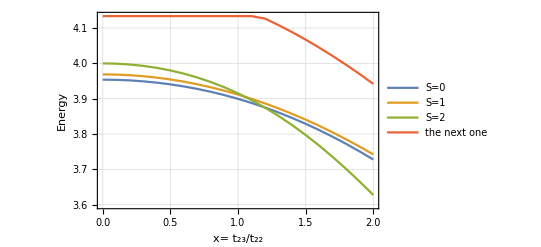

```mathematica
ListLinePlot[{e0data[[1;;21,1;;2]],e1data[[1;;21,1;;2]],e2data[[1;;21,1;;2]],e4data[[1;;21,1;;2]]},PlotLegends->{"S=0","S=1","S=2","the next one"},Frame->True,GridLines->Automatic,AxesLabel->{"x= t_23/t_22","Energy"}]
```

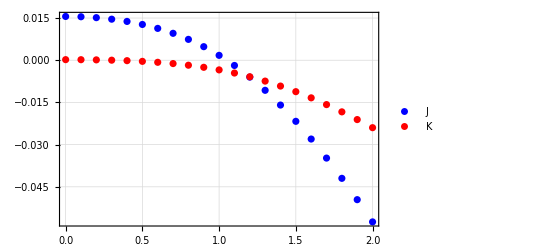

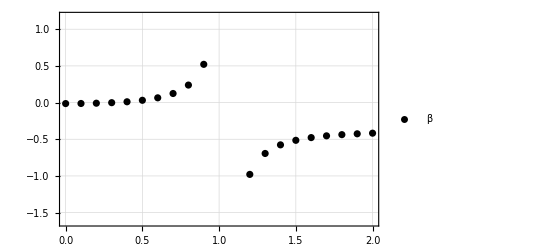

```mathematica
jj1=Table[{e2data[[i,1]],(e2data[[i,2]]-e1data[[i,2]])/2},{i,1,Dimensions[e1data][[1]]}];
jj2=Table[{e2data[[i,1]],e0data[[i,2]]/3.0+e2data[[i,2]]/6.0-e1data[[i,2]]/2.0},{i,1,Dimensions[e1data][[1]]}];
beta=Table[{e2data[[i,1]],-jj2[[i,2]]/jj1[[i,2]]},{i,1,Dimensions[jj1][[1]]}];
ListPlot[{jj1,jj2},PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"J","K"},{Left,Center}],PlotStyle->{Blue,Red}]
ListPlot[beta,PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"β"},{Left,Center}],PlotStyle->Black]
```